# Introduction to Computational Physical Chemistry

© 2017 by Joshua Schrier and University Science Books  (Version: 25 July 2017)
Publisher’s Website: http://www.uscibooks.com/schrier.htm

## Chapter 10 - Classical Gas Laws

## 10.1 EQUATIONS OF STATE FOR NON IDEAL GASES

### 10.1.1 Van der Waals equation of state

```mathematica
R=8.314472*10^-2;(*in L.bar/mol.K*)
vdwP[Vm_,T_,a_,b_]:=(R*T/(Vm-b))-(a/Vm^2)
```

```mathematica
vdwP[0.100,300.,1.37,0.0387] (*result in units of bar*)
```

269.907

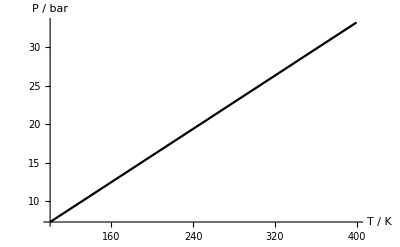

```mathematica
Vm=1;(*e.g.,consider 1 L/mol*)
Plot[ vdwP[Vm,T,1.37,0.0387],{T,100,400},
AxesLabel->{"T / K","P / bar"}]
```

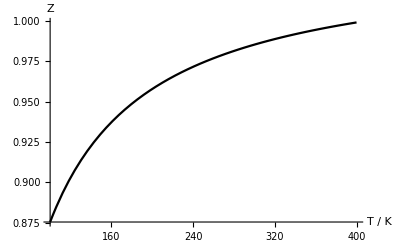

```mathematica
Vm=1;
Plot[ (vdwP[Vm,T,1.37,0.0387]*Vm)/(R*T),{T,100,400},
AxesLabel->{"T / K","Z"}]
```

```mathematica
vdwConstA[Tc_,Pc_]:=27*(R*Tc)^2/(64*Pc) 
vdwConstB[Tc_,Pc_]:=R*Tc/(8*Pc)
```

```mathematica
aN2=vdwConstA[126.21,33.9]
bN2=vdwConstB[126.21,33.9]
```

1.37038

0.0386936

```mathematica
vdwP[0.1,300,aN2,bN2]
```

269.827

```mathematica
vdwP[0.1,300,vdwConstA[126.21,33.9],vdwConstB[126.21,33.9] ]
```

269.827

### 10.1.2 Redlich-Kwong equation of state

```mathematica
rkP[Vm_,T_,a_,b_]:=(R*T/(Vm-b))-(a/(Sqrt[T]*Vm*(Vm+b))) 
rkConstA[Tc_,Pc_]:=0.42748*R^2*Tc^2.5/Pc
rkConstB[Tc_,Pc_]:=0.08662*R*Tc/Pc
```

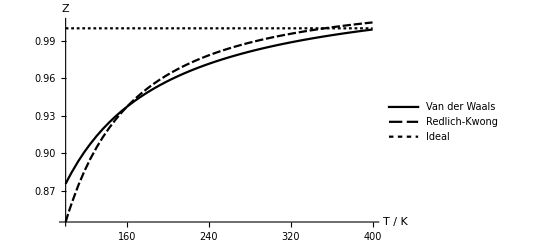

```mathematica
Vm=1;
Plot[
{(vdwP[Vm,T,vdwConstA[126.21,33.9],vdwConstB[126.21,33.9]]*Vm)/(R*T),(rkP[Vm,T,rkConstA[126.21,33.9],rkConstB[126.21,33.9]]*Vm)/(R*T),
1},
{T,100,400},
AxesLabel->{"T / K","Z"},
PlotLegends->{"Van der Waals","Redlich-Kwong","Ideal"}]
```

### 10.2 USING CHEMICALDATA[] TO OBTAIN MOLECULAR CONSTANTS

```mathematica
ChemicalData["Nitrogen","VanDerWaalsConstants"]
```

{1.37 bar L^2/mol^2,0.0387 L/mol}

```mathematica
ChemicalData["Nitrogen","CriticalTemperature"]
```

126.21 K

```mathematica
ChemicalData["Nitrogen","CriticalPressure"]
```

3.39 MPa

```mathematica
QuantityMagnitude[ ChemicalData["Nitrogen","CriticalPressure"] ]
```

3.39

```mathematica
QuantityUnit[ ChemicalData["Nitrogen","CriticalPressure"] ]
```

Megapascals

```mathematica
vdwConstA[
QuantityMagnitude[ ChemicalData["Nitrogen","CriticalTemperature"] ],QuantityMagnitude[ ChemicalData["Nitrogen","CriticalPressure"] ]*10 ]
```

1.37038

```mathematica
R=Quantity[8.314472*10^-2,("Liters"*"Bars")/("Moles"*"Kelvins")]
```

0.0831447 bar L/(K mol)

```mathematica
vdwConstA[
ChemicalData["Nitrogen","CriticalTemperature"],ChemicalData["Nitrogen","CriticalPressure"] ]
```

1.37038 bar L^2/mol^2

## 10.3 SOLVING EQUATIONS: SYMBOLIC VERSUS NUMERICAL APPROACHES

### 10.3.1 Symbolic equation solving

```mathematica
Clear[P,Vm,T,R,a,b]
Solve[(P+a*Vm^-2)*(Vm-b)==R*T,P]
```

{{P→(-a b+a Vm-R T Vm^2)/((b-Vm) Vm^2)}}

```mathematica
FullSimplify[%]
```

{{P→-a/Vm^2+(R T)/(-b+Vm)}}

### 10.3.2 Numerical equation solving

```mathematica
Solve[(P+a*Vm^-2)*(Vm-b)==R*T,Vm] (*lots of output...*)
```

{{Vm→-(-b P-R T)/(3 P)-(2^(1/3) (3 a P-(-b P-R T)^2))/(3 P (18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3+√((18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3)^2+4 (3 a P-(-b P-R T)^2)^3))^(1/3))+1/(3 2^(1/3) P)(18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3+√((18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3)^2+4 (3 a P-(-b P-R T)^2)^3))^(1/3)},{Vm→-(-b P-R T)/(3 P)+((1+ⅈ √3) (3 a P-(-b P-R T)^2))/(3 2^(2/3) P (18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3+√((18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3)^2+4 (3 a P-(-b P-R T)^2)^3))^(1/3))-1/(6 2^(1/3) P)(1-ⅈ √3) (18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3+√((18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3)^2+4 (3 a P-(-b P-R T)^2)^3))^(1/3)},{Vm→-(-b P-R T)/(3 P)+((1-ⅈ √3) (3 a P-(-b P-R T)^2))/(3 2^(2/3) P (18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3+√((18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3)^2+4 (3 a P-(-b P-R T)^2)^3))^(1/3))-1/(6 2^(1/3) P)(1+ⅈ √3) (18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3+√((18 a b P^2+2 b^3 P^3-9 a P R T+6 b^2 P^2 R T+6 b P R^2 T^2+2 R^3 T^3)^2+4 (3 a P-(-b P-R T)^2)^3))^(1/3)}}

```mathematica
R=8.314472*10−2;(*in L.bar/mol.K*)
NSolve[ vdwP[Vm,300,1.37,0.0387]==269.827,Vm] (*in L/mol*)
```

{{Vm→90.2573},{Vm→0.0000281149+0.00147521 ⅈ},{Vm→0.0000281149-0.00147521 ⅈ}}

```mathematica
R=8.314472*10^-2;(*in L.bar/mol.K*)
FindRoot[vdwP[Vm,300,1.37,0.0387]==269.827,{Vm,1}] (*L/mol*)
```

{Vm→0.100021}

## 10.4 EXAMPLES

### 10.4.1 Critical points of the van der Waals gas

```mathematica
Clear[V,R,T,P,a,b] (*we want these as symbolic constants*) 
firstDeriv=FullSimplify[ D[ vdwP[V,T,a,b],V] ]
```

-(R T)/(b-V)^2+(2 a)/V^3

```mathematica
secondDeriv=FullSimplify[ D[ vdwP[V,T,a,b],{V,2}] ]
```

-(6 a)/V^4+(2 R T)/(-b+V)^3

```mathematica
solution2=Solve[{firstDeriv==0,secondDeriv==0},{V,T}]
```

{{V→3 b,T→(8 a)/(27 b R)}}

```mathematica
solution2[[1]]
```

{V→3 b,T→(8 a)/(27 b R)}

```mathematica
solution2[[1,1]]
```

V→3 b

```mathematica
solution2[[1,1,2]]
```

3 b

```mathematica
Subscript[V, c]=solution2[[1,1,2]];
Subscript[T, c]=solution2[[1,2,2]];
Subscript[P, c]=vdwP[Subscript[V, c],Subscript[T, c],a,b]
```

a/(27 b^2)

### 10.4.2 The law of corresponding states

```mathematica
FullSimplify[
Solve[Subscript[P, c]*Subscript[P, r]==vdwP[Subscript[V, c]*Subscript[V, r],Subscript[T, c]*Subscript[T, r],a,b],Subscript[P, r]]]
```

{{P_r→-3/V_r^2+(8 T_r)/(-1+3 V_r)}}

### 10.4.3 Reversible expansion/compression work

```mathematica
Tc=QuantityMagnitude[ChemicalData["Nitrogen","CriticalTemperature"]];Pc=QuantityMagnitude[ChemicalData["Nitrogen","CriticalPressure"]]*10;R=8.314472*10^-2;(*in L.bar/mol.K*)

NIntegrate[  (*w = ∫_Subscript[V, i]^Subscript[V, f] -P ⅆV*)
-vdwP[V,300,vdwConstA[Tc,Pc],vdwConstB[Tc,Pc]] (*integrand*)
,{V,1,0.1} (*limits of integration*)
] (*results in units of L.bar=100 joules*)
```

56.321

```mathematica
NIntegrate[ -rkP[V,300,rkConstA[Tc,Pc],rkConstB[Tc,Pc]],{V,1,0.1}]
```

57.4522

```mathematica
NIntegrate[ -(R*300/V),{V,1,0.1}]
```

57.4343